```mathematica
Quit[]
```

```mathematica
With[{pts={{0,0,0},{1,0,0},{0,1,0},{1,0,1},{0,1,1},{1,1,1}},fcs={{1,2,3},{4,5,6},{1,2,4},{1,3,5},{2,3,6},{1,4,5},{3,5,6},{2,4,6}}},Graphics3D[{Opacity[0.9],Texture[-Graphics-],Polyhedron[pts[[Sequence@#]]&/@fcs,VertexTextureCoordinates->(pts[[Sequence@#]]&/@fcs)]}]]
```

-Graphics3D-

```mathematica
With[{pts={{0,0,0},{1,0,0},{0,1,0},{1,0,1},{0,1,1},{1,1,1}},fcs={{1,2,3},{4,5,6},{1,2,4},{1,3,5},{2,3,6},{1,4,5},{3,5,6},{2,4,6}}},pts[[Sequence@#]]&/@fcs]
```

{{{0,0,0},{1,0,0},{0,1,0}},{{1,0,1},{0,1,1},{1,1,1}},{{0,0,0},{1,0,0},{1,0,1}},{{0,0,0},{0,1,0},{0,1,1}},{{1,0,0},{0,1,0},{1,1,1}},{{0,0,0},{1,0,1},{0,1,1}},{{0,1,0},{0,1,1},{1,1,1}},{{1,0,0},{1,0,1},{1,1,1}}}

```mathematica
Inverse[{{1,0,1},{0,1,1},{1,1,1}}ᵀ]
```

{{0,-1,1},{-1,0,1},{1,1,-1}}

```mathematica
Graphics3D[Arrow[{{0,0,0},#}]&/@(Tuples[{0,1},3].%32)]
```

-Graphics3D-

Are there any arrangement acheiving maximum product except for cube-with-basis? achNumber counts number of such arrangements given a non-degenerate 0-1 matrix -- basis of the second set in the coordinates dual to some basis of the second set. If maximum is only acheived with cube+basis, the function will return 2

```mathematica
$HistoryLength=1
```

1

```mathematica
achNumber[B01_List]:=With[{Cpl=Complement,Len=Length,d=Length@B01,cube=Tuples[{0,1},Length@B01],inv=Inverse[B01]},With[{acan=Select[Subsets[Cpl[cube,B01]],Divisible[2^d(d+1),(Len@#+d)]&],bcan=Select[Subsets[Cpl[cube,B01ᵀ]],Divisible[2^d(d+1),(Len@#+d)]&]},Total@Flatten@Table[Boole[Cpl[Flatten[Join[B01,a].inv.(Join[B01ᵀ,b]ᵀ)],{0,1}]=={}],{a,acan},{b,Select[bcan,Len@#==(2^d(d+1))/(d+Len@a)-d&]}]]]
```

Test on all invertible 2 x2 matrices :

```mathematica
Tally[achNumber/@Select[Tuples[{0,1},{2,2}],MatrixRank@#==2&]]//AbsoluteTiming
```

{0.0036872,{{2,6}}}

Test on all invertible 3x3 matrices:

```mathematica
Tally[achNumber/@Select[Tuples[{0,1},{3,3}],MatrixRank@#==3&]]//AbsoluteTiming
```

{0.140387,{{2,174}}}

Number of 4x4 basises ignoring order:

```mathematica
Select[DeleteDuplicates[Sort/@Tuples[{0,1},{4,4}]],MatrixRank@#==4&]//Length
```

940

```mathematica
achNumber[IdentityMatrix[4]]//AbsoluteTiming
```

{15.8582,2}

```mathematica
35*940/3600.
```

9.13889

```mathematica
SeedRandom[42];fourByFourSample=Transpose/@RandomSample[Select[DeleteDuplicates[Sort/@Tuples[{0,1},{4,4}]],MatrixRank@#==4&],4]
```

{{{0,0,1,1},{0,1,0,0},{1,0,0,1},{1,0,1,0}},{{0,0,0,1},{0,1,1,0},{0,0,1,1},{1,1,0,0}},{{0,0,0,1},{0,0,1,1},{0,1,0,0},{1,1,1,0}},{{0,0,1,1},{0,1,0,1},{0,1,1,0},{1,1,1,0}}}

```mathematica
(achNumber/@fourByFourSample)//AbsoluteTiming
```

{565.683,{2,2,2,2}}

```mathematica
matrixPicture[B01_]:=Module[{d=Length@B01,cube,final,pos1,pos2},cube=Tuples[{0,1},d];pos1=Flatten[Position[cube,#]&/@(B01ᵀ)]; pos2=Flatten[Position[cube,#]&/@B01];final=cube.Inverse@B01.(cubeᵀ);
Style[{ArrayPlot[final,ColorRules->{0->GrayLevel[0],1->RGBColor[0.2, 0.2, 0.2]},ColorFunction->(ColorData["Rainbow",(#+1)/2]&),Epilog->{Black,MapIndexed[Text[#1,Reverse[#2-0.5]]&,Reverse[final],{2}],RGBColor[0.23, 0.94, 1],Arrow[{{#-0.5,2^d},{#-0.5,2^d-1/2}}]&/@pos1,Arrow[{{0,2^d-#+0.5},{0.5,2^d-#+0.5}}]&/@pos2},ImageSize->300,Frame->None,Background->White,PlotRangePadding->0.1],Style[B01//MatrixForm,White]},White,Background->Black]]
```

```mathematica
matrixPicture[{{1,0,1},{0,1,1},{0,0,1}}]//Rasterize
```

-Graphics-

```mathematica
matrixPicture[IdentityMatrix@3]//Rasterize
```

-Graphics-

```mathematica
matrixPicture@First[RandomChoice[Select[Tuples[{0,1},{3,3}],MatrixRank@#==3&],1]]//Rasterize
```

-Graphics-

```mathematica
imlist=Rasterize/@matrixPicture/@Select[Tuples[{0,1},{3,3}],MatrixRank@#==3&];
```

```mathematica
matrixPicture@IdentityMatrix[4]//Rasterize
```

-Graphics-

```mathematica
NestWhile[RandomChoice[{0,1},{4,4}]&,{{0}},MatrixRank[#]!=4&]
```

{{0,1,1,1},{1,0,0,1},{0,1,1,0},{0,1,0,1}}

```mathematica
matrixPicture@%//Rasterize
```

-Graphics-

```mathematica
Inverse@{{0,1,1,1},{1,0,0,1},{0,1,1,0},{0,1,0,1}}
```

{{-1,1,1,0},{-1,0,1,1},{1,0,0,-1},{1,0,-1,0}}

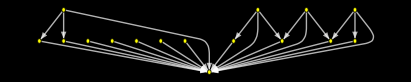

```mathematica
Graph[graphPicture@{{0,1,1,1},{1,0,0,1},{0,1,1,0},{0,1,0,1}},Background->Black,VertexStyle->Yellow,EdgeStyle->White]
```

```mathematica
Graph[graphFullSym@IdentityMatrix[3]]
```

-Graphics-

Check wether sets of “skewed dot products” coincide with all nonbinary inputs treated as same and no distinction between 0 and 1:

```mathematica
coincidingSets[B01_]:=Module[{d=Length@B01,cube,final},cube=Tuples[{0,1},d];final=cube.Inverse@B01.(cubeᵀ)/.{1->0,x_/;x!=0->2};Map[Sort,final,{0,-2}]==Map[Sort,finalᵀ,{0,-2}]]
```

Check on invertible d*d matrices for d from 2 to 4:

```mathematica
Table[And@@coincidingSets/@Select[Tuples[{0,1},{d,d}],MatrixRank@#==d&],{d,2,4}]
```

{True,True,True}

```mathematica
randomInvertible[d_]:=NestWhile[RandomChoice[{0,1},{d,d}]&,{{0}},MatrixRank[#]!=d&]
```

```mathematica
randomInvertible[5]
```

{{1,1,1,0,1},{1,0,0,1,0},{0,1,0,0,0},{1,0,0,1,1},{1,0,0,0,1}}

```mathematica
NotebookDelete[temp]
```

NotebookDelete[temp]

```mathematica
cnt=0;SeedRandom[42];NestWhile[If[Mod[cnt,1]==0,NotebookDelete[temp];temp=PrintTemporary[cnt]];cnt++;randomInvertible[4]&,{{1}},coincidingSets[#]&]
```

$Aborted

```mathematica
counterexample5={{0,0,1,1,1},{0,1,0,0,0},{1,0,0,1,1},{1,1,0,1,0},{1,0,0,0,0}}
```

{{0,0,1,1,1},{0,1,0,0,0},{1,0,0,1,1},{1,1,0,1,0},{1,0,0,0,0}}

```mathematica
coincidingSets@counterexample5
```

False

```mathematica
matrixPicture@counterexample5//Rasterize
```

-Graphics-

```mathematica
cube01[d_]:=Tuples[{0,1},d]
```

```mathematica
Style[With[{cube=Tuples[{0,1},5]},ArrayPlot[Map[Sort,(cube.Inverse[#].(cubeᵀ))/.{1->0,x_/;x!=0->2},{0,-2}],Frame->True,FrameStyle->White,Background->Black,PlotRangePadding->None,Mesh->True,MeshStyle->Directive[GrayLevel[0.27],Thickness[10^-4]],ColorRules->{0->Black,2->Orange}]]&/@{counterexample5,counterexample5ᵀ},White,Background->Black]//Rasterize
```

-Graphics-

```mathematica
Inverse@counterexample5
```

{{0,0,0,0,1},{0,1,0,0,0},{1,0,-1,0,1},{0,-1,0,1,-1},{0,1,1,-1,0}}

Function to produce graph of allowable relations given symmetric invertible 01 matrix:

```mathematica
graphFullSym[B01_]:=Module[{d=Length@B01,cube,matr},cube=Tuples[{0,1},d];matr=(cube.Inverse@B01.(cubeᵀ))/.{1->0,x_/;x!=0->2};
Flatten@Table[If[i!=j&&And@@NonNegative[matr[[i]]-matr[[j]]],cube[[i]]->cube[[j]],Nothing],{i,2^d},{j,2^d}]]
```

```mathematica
allSymInvertible[d_]:=DeleteDuplicatesBy[Select[(#+LowerTriangularize[#ᵀ,-1])&/@PadLeft/@(Internal`PartitionRagged[#,Range[d,1,-1]]&)/@Tuples[{0,1},(d(d+1))/2],MatrixRank@#==d&],Sort]
```

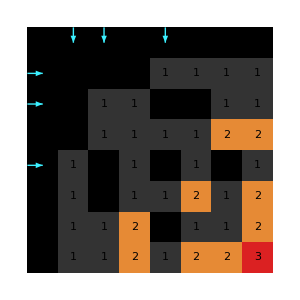
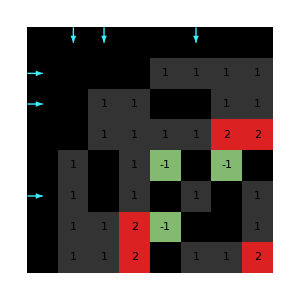
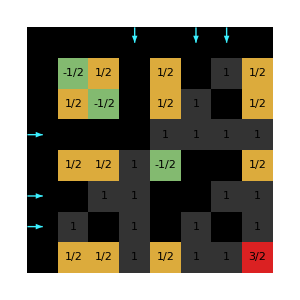
-Graphics- | {-Graphics-,(0 | 0 | 1
0 | 1 | 0
1 | 0 | 0)}
-Graphics- | {-Graphics-,(0 | 0 | 1
0 | 1 | 0
1 | 0 | 1)}
-Graphics- | {-Graphics-,(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0)}

```mathematica
Style[Grid@DeleteDuplicates[{Graph[graphFullSym@#,Background->Black,VertexStyle->White,EdgeStyle->Yellow],matrixPicture@#}&/@allSymInvertible[3],IsomorphicGraphQ[#1[[1]],#2[[1]]]&],Background->Black,White]
```

```mathematica
Inverse@({{0, 0, 1}, {0, 1, 0}, {1, 0, 1}})
```

{{-1,0,1},{0,1,0},{1,0,0}}

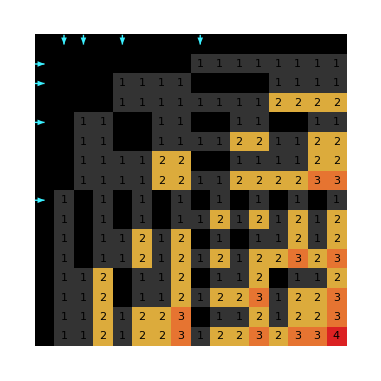
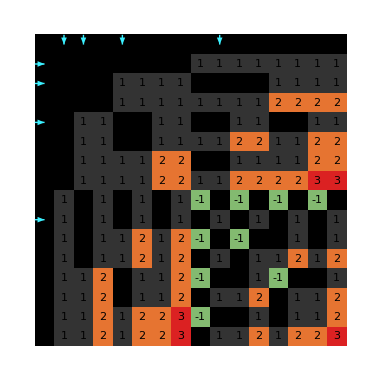
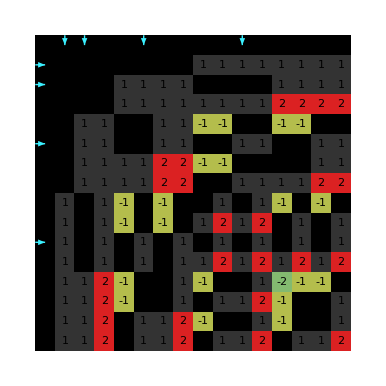
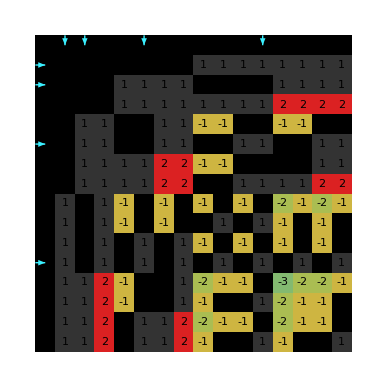
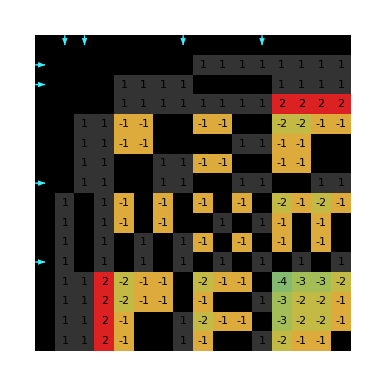
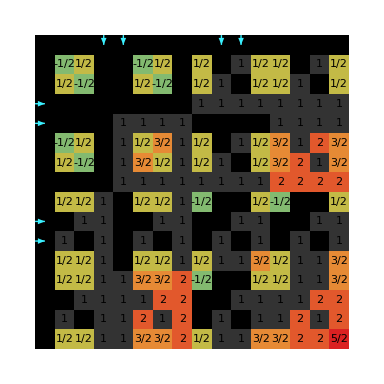
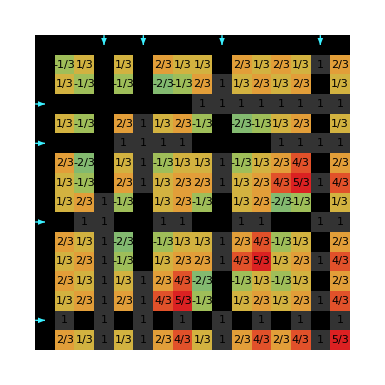
-Graphics- | {-Graphics-,(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)}
-Graphics- | {-Graphics-,(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 1)}
-Graphics- | {-Graphics-,(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0)}
-Graphics- | {-Graphics-,(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 1)}
-Graphics- | {-Graphics-,(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 1 | 1
1 | 0 | 1 | 1)}
-Graphics- | {-Graphics-,(0 | 0 | 1 | 1
0 | 1 | 0 | 0
1 | 0 | 0 | 1
1 | 0 | 1 | 0)}
-Graphics- | {-Graphics-,(0 | 0 | 1 | 1
0 | 1 | 0 | 1
1 | 0 | 0 | 1
1 | 1 | 1 | 0)}

```mathematica
Style[Grid@DeleteDuplicates[{Graph[graphFullSym@#,Background->Black,VertexStyle->White,EdgeStyle->Yellow],matrixPicture@#}&/@allSymInvertible[4],IsomorphicGraphQ[#1[[1]],#2[[1]]]&],Background->Black,White]
```

```mathematica
{Graph[graphFullSym[counterexample5]],Graph[graphFullSym[counterexample5ᵀ]]}
```

{-Graphics-,-Graphics-}

```mathematica
graphSymNoSinks[B01_]:=Module[{d=Length@B01,filtcube,matr,pos},filtcube=Rest@DeleteCases[Tuples[{0,1},d],Alternatives@@B01];matr=(filtcube.Inverse@B01.(filtcubeᵀ))/.{1->0,x_/;x!=0->2};
Flatten@Table[If[i!=j&&And@@NonNegative[matr[[i]]-matr[[j]]],filtcube[[i]]->filtcube[[j]],Nothing],{i,2^d-d-1},{j,2^d-d-1}]]
```

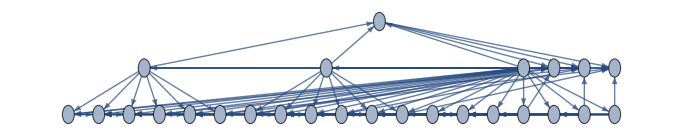

```mathematica
Graph[graphSymNoSinks@IdentityMatrix@5,GraphLayout->"LayeredEmbedding"]
```

```mathematica
graphSymFactorizedAndSzs[B01_]:=Module[{d=Length@B01,cube,grps,filt=(#/.{1->0,x_/;x!=0->2}&)},cube=Tuples[{0,1},d];grps={#,filt[#[[1]]]}&/@GatherBy[cube.Inverse@B01.(cubeᵀ),filt];
{Flatten@Table[If[i!=j&&And@@NonNegative[grps[[i,2]]-grps[[j,2]]],grps[[i,1]]->grps[[j,1]],Nothing],{i,Length@grps},{j,Length@grps}],Normal@AssociationMap[Length,grps[[All,1]]]}]
```

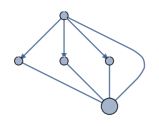

```mathematica
With[{gsf=graphSymFactorizedAndSzs[IdentityMatrix[3]]},Graph[First@gsf,VertexLabels->MapAt[Placed[#,Center]&,gsf[[2]],{All,2}],VertexSize->MapAt[{"Scaled",Sqrt[#]/20}&,gsf[[2]],{All,2}]]]
```

```mathematica
Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"]
```

The currently installed versions of IGraph/M are: {}

Installing IGraph/M is complete: PacletObject[…].

It can now be loaded using the command <<IGraphM`

```mathematica
<<IGraphM`
```

IGraph/M 0.6.5 (December 21, 2022)
Evaluate IGDocumentation[] to get started.

```mathematica
graphSymFactorizedRaw[B01_]:=Module[{d=Length@B01,cube,grps,filt=(#/.{1->0,x_/;x!=0->2}&)},cube=Tuples[{0,1},d];grps={#,filt[#[[1]]]}&/@GatherBy[cube.Inverse@B01.(cubeᵀ),filt];
Flatten@Table[If[i!=j&&And@@NonNegative[grps[[i,2]]-grps[[j,2]]],grps[[i,1]]->grps[[j,1]],Nothing],{i,Length@grps},{j,Length@grps}]]
hasseDiagram[gr_]:=With[{f=EdgeQ[gr,#1->#2]&,s=VertexList[gr]},ResourceFunction["HasseDiagram"][f,s,PerformanceGoal->"Quality"]]
```

```mathematica
addGraphProps[gr_]:=Module[{filt=(#/.{1->0,x_/;x!=0->2}&)},gr//IGVertexMap[Sqrt@*Length,"SqLength"->VertexList]/*IGVertexMap[Length,"Length"->VertexList]/*IGVertexMap[filt[#[[1]]]&,"Filter"->VertexList]/*IGVertexMap[MatrixForm[#ᵀ]&,Tooltip->VertexList]]
grSymFact[B01_]:=addGraphProps[Graph[graphSymFactorizedRaw[B01],PerformanceGoal->"Quality"]]
hasseSymFact[B01_]:=addGraphProps[hasseDiagram@Graph[graphSymFactorizedRaw[B01],PerformanceGoal->"Speed"]]
```

```mathematica
dispFact[gr_]:=gr//IGVertexMap[0.1#&,VertexSize->IGVertexProp["SqLength"]]/*IGVertexMap[Placed[If[#==1,"",#],Center]&,VertexLabels->IGVertexProp["Length"]]
```

```mathematica
dispFact[grSymFact[#]]&/@allSymInvertible[3]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

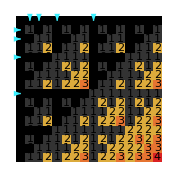
{-Graphics-,(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

```mathematica
matrixPicture@IdentityMatrix[4]
```

```mathematica
dispFact[grSymFact[IdentityMatrix[4]]]
```

-Graphics-

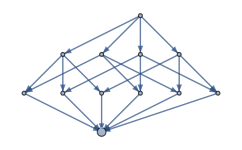

```mathematica
dispFact[hasseSymFact[IdentityMatrix@4]]
```

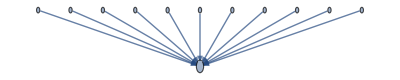
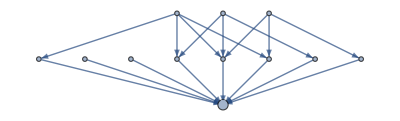
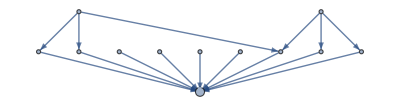
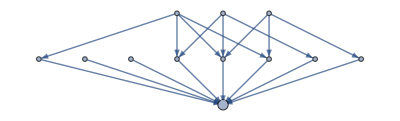
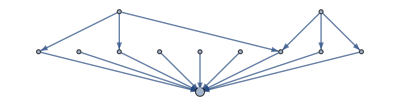
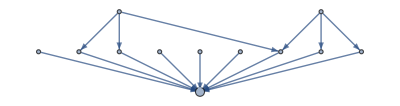
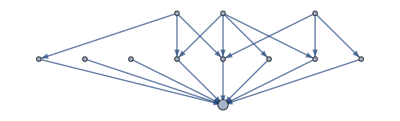
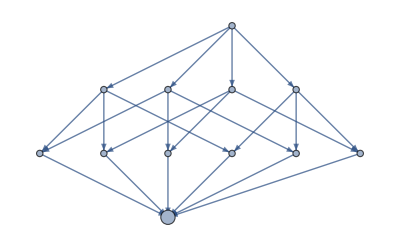
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(dispFact@*hasseSymFact)/@RandomSample[allSymInvertible[4],30]
```

```mathematica
deepSort[expr_]:=Map[Sort,expr,{0,-2}]
```

```mathematica
allSymInvertibleDiffGraph[d_]:=First/@DeleteDuplicates[{#,Graph@graphFullSym@#}&/@allSymInvertible[d],IsomorphicGraphQ[#1[[2]],#2[[2]]]&]
```

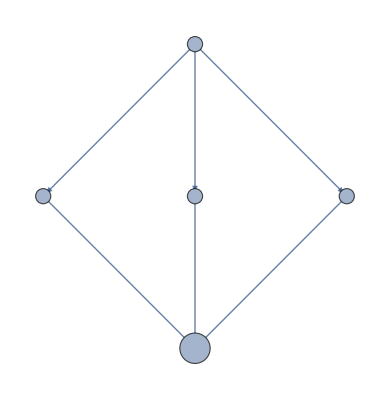
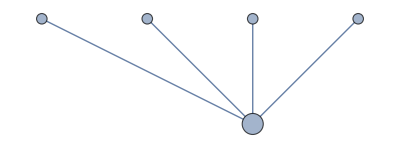
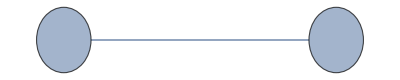

```mathematica
allThreeHasse=dispFact/@hasseSymFact/@allSymInvertibleDiffGraph[3]
```

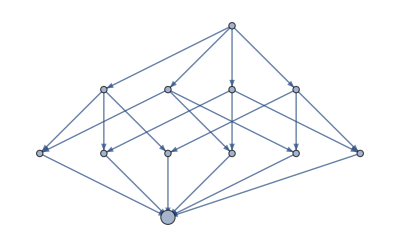
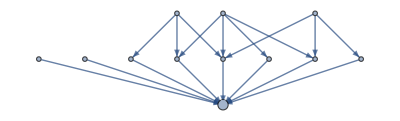
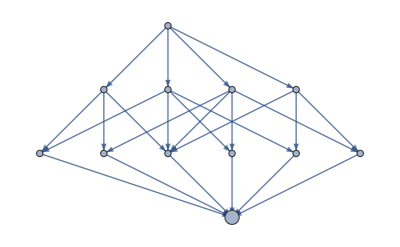
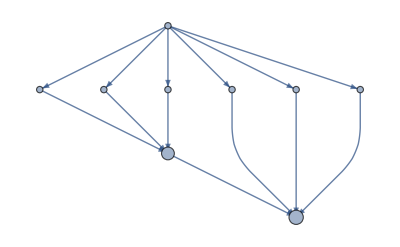
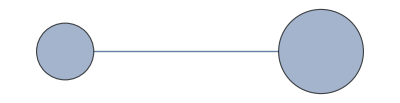
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
allFourHasse=dispFact/@hasseSymFact/@allSymInvertibleDiffGraph[4]
```

```mathematica
setGraphStyle[graph_Graph]:=Graph[graph,EdgeStyle->Yellow,VertexStyle->White,Background->Black,PerformanceGoal->"Quality"]
```

```mathematica
Grid[ArrayReshape[setGraphStyle/@(allFourHasse~Join~allThreeHasse),{5,2}],Background->Black]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"All-Hasse-3-4-diagrams.jpg"}],-Graphics-];
```

```mathematica
allHasse5withDup=ParallelMap[hasseSymFact,allSymInvertible[5]];
```

```mathematica
allFiveHasse=DeleteDuplicates[allHasse5withDup,IsomorphicGraphQ];
```

```mathematica
Grid[ArrayReshape[setGraphStyle/@(allFourHasse~Join~allThreeHasse),{5,2}],Background->Black]
```

```mathematica
DumpSave[FileNameJoin[{NotebookDirectory[],"all-sym-hasse-3.mx"}],allThreeHasse];DumpSave[FileNameJoin[{NotebookDirectory[],"all-sym-hasse-4.mx"}],allFourHasse];DumpSave[FileNameJoin[{NotebookDirectory[],"all-sym-hasse-5.mx"}],allFiveHasse];
```

```mathematica
MapIndexed[Export[FileNameJoin[{NotebookDirectory[],"all-sym-hasse-5-pictures",ToString[#2[[1]]]<>".jpg"}],#1]&,setGraphStyle[Graph[dispFact@#,ImageSize->800]]&/@allFiveHasse];
```

There is an example that is not even a semilattice among 4 by 4 matrices

```mathematica
nonSemilatticecCounter=allSymInvertibleDiffGraph[4][[4]]
```

{{0,0,0,1},{0,0,1,0},{0,1,0,1},{1,0,1,1}}

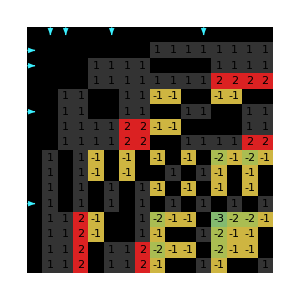
{{-Graphics-,(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 1)},-Graphics-}

```mathematica
Style[{matrixPicture[nonSemilatticecCounter],Graph[setGraphStyle@dispFact@hasseSymFact@nonSemilatticecCounter,ImageSize->400]},Background->Black]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],""}],%288]
```